```mathematica
Clear["Global`*"]
```

```mathematica
potential=40*(x^-12-x^-6);
xstart=2^(1/6);
xmin=0;
xmax=30;
```

```mathematica
psi1[e_?NumericQ,deriv_?NumericQ,stopValueFlag_:False]:=Block[{psi,sol,stop=None},sol=NDSolveValue[{-1/2*psi''[x]+potential*psi[x]==e*psi[x],psi[xstart]==1,psi'[xstart]==deriv,WhenEvent[Abs[psi[x]]==10,{stop={x,psi[x]},"StopIntegration"}]},psi,{x,xmin,xstart}];
If[stopValueFlag,stop/.{{x_,y_}:>y,None:>sol[xmin]},{sol,stop/.None:>{xmin,sol[xmin]}}]];
psi2[e_?NumericQ,deriv_?NumericQ,stopValueFlag_:False]:=Block[{psi,sol,stop=None},sol=NDSolveValue[{-1/2*psi''[x]+potential*psi[x]==e*psi[x],psi[xstart]==1,psi'[xstart]==deriv,WhenEvent[Abs[psi[x]]==10,{stop={x,psi[x]},"StopIntegration"}]},psi,{x,xstart,xmax}];
If[stopValueFlag,stop/.{{x_,y_}:>y,None:>sol[xmax]},{sol,stop/.None:>{xmin,sol[xmin]}}]];
```

```mathematica
Manipulate[Block[{fpsi1,fpsi2},
fpsi1=psi1[e,deriv];fpsi2=psi2[e,deriv];Plot[{Piecewise[{{fpsi1[[1]][x],x<xstart},{fpsi2[[1]][x],x>=xstart}}],potential,e},{x,fpsi1[[2,1]],fpsi2[[2,1]]},PlotRange->{{xmin,xmax},{-10,10}}]],{{e,-0.5},-2,0},{{deriv,0},-10,10}]
```

```mathematica
deriv1[e_?NumericQ]:=Block[{deriv},deriv/.FindRoot[psi1[e,deriv,True],{deriv,-10,10},Method->"Brent"]]
deriv2[e_?NumericQ]:=Block[{deriv},deriv/.FindRoot[psi2[e,deriv,True],{deriv,-10,10},Method->"Brent"]]
Off[FindRoot::brmp]
```

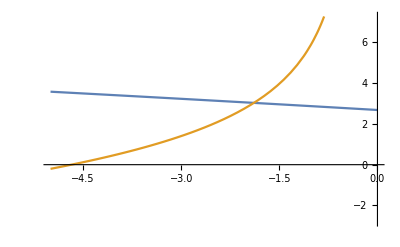

```mathematica
Plot[{deriv1[e],deriv2[e]},{e,-5,0}]
```

```mathematica
energy=e/.FindRoot[deriv1[e]==deriv2[e],{e,-2,-1},Method->"Brent"]
```

-1.8899

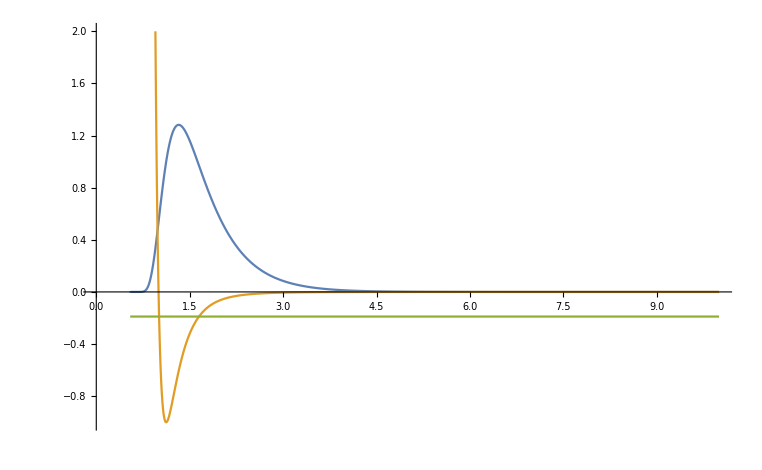

```mathematica
Block[{fpsi1,fpsi2},
fpsi1=psi1[energy,deriv1[energy]];fpsi2=psi2[energy,deriv2[energy]];Plot[{Piecewise[{{fpsi1[[1]][x],x<xstart},{fpsi2[[1]][x],x>=xstart}}],potential/10,energy/10},{x,fpsi1[[2,1]]+0.02,10},PlotRange->{-1,2},Exclusions->None]]
```